### Load energy density

```mathematica
wd=SetDirectory@NotebookDirectory[];
e0500dat=Import[wd<>"/e_0.500.dat"];
e1000dat=Import[wd<>"/e_1.000.dat"];
e1500dat=Import[wd<>"/e_1.500.dat"];
e2000dat=Import[wd<>"/e_2.000.dat"];
e2500dat=Import[wd<>"/e_2.500.dat"];
e3000dat=Import[wd<>"/e_3.000.dat"];
e3500dat=Import[wd<>"/e_3.500.dat"];
e4000dat=Import[wd<>"/e_4.000.dat"];
e4500dat=Import[wd<>"/e_4.500.dat"];
e5000dat=Import[wd<>"/e_5.000.dat"];
e5500dat=Import[wd<>"/e_5.500.dat"];
e6000dat=Import[wd<>"/e_6.000.dat"];
e6500dat=Import[wd<>"/e_6.500.dat"];
e7000dat=Import[wd<>"/e_7.000.dat"];
e7500dat=Import[wd<>"/e_7.500.dat"];
e8000dat=Import[wd<>"/e_8.000.dat"];
e8500dat=Import[wd<>"/e_8.500.dat"];
e9000dat=Import[wd<>"/e_9.000.dat"];
e9500dat=Import[wd<>"/e_9.500.dat"];
e10000dat=Import[wd<>"/e_10.000.dat"];
e10500dat=Import[wd<>"/e_10.500.dat"];
e11000dat=Import[wd<>"/e_11.000.dat"];
```

### Load bulk pressure

```mathematica
wd=SetDirectory@NotebookDirectory[];
Pi0500dat=Import[wd<>"/Pi_0.500.dat"];
Pi1000dat=Import[wd<>"/Pi_1.000.dat"];
Pi1500dat=Import[wd<>"/Pi_1.500.dat"];
Pi2000dat=Import[wd<>"/Pi_2.000.dat"];
Pi2500dat=Import[wd<>"/Pi_2.500.dat"];
Pi3000dat=Import[wd<>"/Pi_3.000.dat"];
Pi3500dat=Import[wd<>"/Pi_3.500.dat"];
Pi4000dat=Import[wd<>"/Pi_4.000.dat"];
Pi4500dat=Import[wd<>"/Pi_4.500.dat"];
Pi5000dat=Import[wd<>"/Pi_5.000.dat"];
Pi5500dat=Import[wd<>"/Pi_5.500.dat"];
Pi6000dat=Import[wd<>"/Pi_6.000.dat"];
Pi6500dat=Import[wd<>"/Pi_6.500.dat"];
Pi7000dat=Import[wd<>"/Pi_7.000.dat"];
Pi7500dat=Import[wd<>"/Pi_7.500.dat"];
Pi8000dat=Import[wd<>"/Pi_8.000.dat"];
Pi8500dat=Import[wd<>"/Pi_8.500.dat"];
Pi9000dat=Import[wd<>"/Pi_9.000.dat"];
Pi9500dat=Import[wd<>"/Pi_9.500.dat"];
Pi10000dat=Import[wd<>"/Pi_10.000.dat"];
Pi10500dat=Import[wd<>"/Pi_10.500.dat"];
Pi11000dat=Import[wd<>"/Pi_11.000.dat"];
```

### Energy tau-x data

```mathematica
e0500dat=e0500dat[[All,{1,2,4}]];
e1000dat=e1000dat[[All,{1,2,4}]];
e1500dat=e1500dat[[All,{1,2,4}]];
e2000dat=e2000dat[[All,{1,2,4}]];
e2500dat=e2500dat[[All,{1,2,4}]];
e3000dat=e3000dat[[All,{1,2,4}]];
e3500dat=e3500dat[[All,{1,2,4}]];
e4000dat=e4000dat[[All,{1,2,4}]];
e4500dat=e4500dat[[All,{1,2,4}]];
e5000dat=e5000dat[[All,{1,2,4}]];
e5500dat=e5500dat[[All,{1,2,4}]];
e6000dat=e6000dat[[All,{1,2,4}]];
e6500dat=e6500dat[[All,{1,2,4}]];
e7000dat=e7000dat[[All,{1,2,4}]];
e7500dat=e7500dat[[All,{1,2,4}]];
e8000dat=e8000dat[[All,{1,2,4}]];
e8500dat=e8500dat[[All,{1,2,4}]];
e9000dat=e9000dat[[All,{1,2,4}]];
e9500dat=e9500dat[[All,{1,2,4}]];
e10000dat=e10000dat[[All,{1,2,4}]];
e10500dat=e10500dat[[All,{1,2,4}]];
e11000dat=e11000dat[[All,{1,2,4}]];

j = 64;(* y-index for y = 0.0*)
e0500=Table[{e0500dat[[i+127*(j-1),1]],0.5,e0500dat[[i+127*(j-1),3]]},{i,1,127}];
e1000=Table[{e1000dat[[i+127*(j-1),1]],1.0,e1000dat[[i+127*(j-1),3]]},{i,1,127}];
e1500=Table[{e1500dat[[i+127*(j-1),1]],1.5,e1500dat[[i+127*(j-1),3]]},{i,1,127}];
e2000=Table[{e2000dat[[i+127*(j-1),1]],2.0,e2000dat[[i+127*(j-1),3]]},{i,1,127}];
e2500=Table[{e2500dat[[i+127*(j-1),1]],2.5,e2500dat[[i+127*(j-1),3]]},{i,1,127}];
e3000=Table[{e3000dat[[i+127*(j-1),1]],3.0,e3000dat[[i+127*(j-1),3]]},{i,1,127}];
e3500=Table[{e3500dat[[i+127*(j-1),1]],3.5,e3500dat[[i+127*(j-1),3]]},{i,1,127}];
e4000=Table[{e4000dat[[i+127*(j-1),1]],4.0,e4000dat[[i+127*(j-1),3]]},{i,1,127}];
e4500=Table[{e4500dat[[i+127*(j-1),1]],4.5,e4500dat[[i+127*(j-1),3]]},{i,1,127}];
e5000=Table[{e5000dat[[i+127*(j-1),1]],5.0,e5000dat[[i+127*(j-1),3]]},{i,1,127}];
e5500=Table[{e5500dat[[i+127*(j-1),1]],5.5,e5500dat[[i+127*(j-1),3]]},{i,1,127}];
e6000=Table[{e6000dat[[i+127*(j-1),1]],6.0,e6000dat[[i+127*(j-1),3]]},{i,1,127}];
e6500=Table[{e6500dat[[i+127*(j-1),1]],6.5,e6500dat[[i+127*(j-1),3]]},{i,1,127}];
e7000=Table[{e7000dat[[i+127*(j-1),1]],7.0,e7000dat[[i+127*(j-1),3]]},{i,1,127}];
e7500=Table[{e7500dat[[i+127*(j-1),1]],7.5,e7500dat[[i+127*(j-1),3]]},{i,1,127}];
e8000=Table[{e8000dat[[i+127*(j-1),1]],8.0,e8000dat[[i+127*(j-1),3]]},{i,1,127}];
e8500=Table[{e8500dat[[i+127*(j-1),1]],8.5,e8500dat[[i+127*(j-1),3]]},{i,1,127}];
e9000=Table[{e9000dat[[i+127*(j-1),1]],9.0,e9000dat[[i+127*(j-1),3]]},{i,1,127}];
e9500=Table[{e9500dat[[i+127*(j-1),1]],9.5,e9500dat[[i+127*(j-1),3]]},{i,1,127}];
e10000=Table[{e10000dat[[i+127*(j-1),1]],10.0,e10000dat[[i+127*(j-1),3]]},{i,1,127}];
e10500=Table[{e10500dat[[i+127*(j-1),1]],10.5,e10500dat[[i+127*(j-1),3]]},{i,1,127}];
e11000=Table[{e11000dat[[i+127*(j-1),1]],11.0,e11000dat[[i+127*(j-1),3]]},{i,1,127}];

eplot = Join[e0500,e1000,e1500,e2000,e2500,e3000,e3500,e4000,e4500,e5000,e5500,e6000,e6500,e7000,e7500,e8000,e8500,e9000,e9500,e10000,e10500,e11000];
```

### Bulk pressure tau-x data

```mathematica
Pi0500dat=Pi0500dat[[All,{1,2,4}]];
Pi1000dat=Pi1000dat[[All,{1,2,4}]];
Pi1500dat=Pi1500dat[[All,{1,2,4}]];
Pi2000dat=Pi2000dat[[All,{1,2,4}]];
Pi2500dat=Pi2500dat[[All,{1,2,4}]];
Pi3000dat=Pi3000dat[[All,{1,2,4}]];
Pi3500dat=Pi3500dat[[All,{1,2,4}]];
Pi4000dat=Pi4000dat[[All,{1,2,4}]];
Pi4500dat=Pi4500dat[[All,{1,2,4}]];
Pi5000dat=Pi5000dat[[All,{1,2,4}]];
Pi5500dat=Pi5500dat[[All,{1,2,4}]];
Pi6000dat=Pi6000dat[[All,{1,2,4}]];
Pi6500dat=Pi6500dat[[All,{1,2,4}]];
Pi7000dat=Pi7000dat[[All,{1,2,4}]];
Pi7500dat=Pi7500dat[[All,{1,2,4}]];
Pi8000dat=Pi8000dat[[All,{1,2,4}]];
Pi8500dat=Pi8500dat[[All,{1,2,4}]];
Pi9000dat=Pi9000dat[[All,{1,2,4}]];
Pi9500dat=Pi9500dat[[All,{1,2,4}]];
Pi10000dat=Pi10000dat[[All,{1,2,4}]];
Pi10500dat=Pi10500dat[[All,{1,2,4}]];
Pi11000dat=Pi11000dat[[All,{1,2,4}]];

j = 64;(* y-index for y = 0.0*)
Pi0500=Table[{Pi0500dat[[i+127*(j-1),1]],0.5,Pi0500dat[[i+127*(j-1),3]]},{i,1,127}];
Pi1000=Table[{Pi1000dat[[i+127*(j-1),1]],1.0,Pi1000dat[[i+127*(j-1),3]]},{i,1,127}];
Pi1500=Table[{Pi1500dat[[i+127*(j-1),1]],1.5,Pi1500dat[[i+127*(j-1),3]]},{i,1,127}];
Pi2000=Table[{Pi2000dat[[i+127*(j-1),1]],2.0,Pi2000dat[[i+127*(j-1),3]]},{i,1,127}];
Pi2500=Table[{Pi2500dat[[i+127*(j-1),1]],2.5,Pi2500dat[[i+127*(j-1),3]]},{i,1,127}];
Pi3000=Table[{Pi3000dat[[i+127*(j-1),1]],3.0,Pi3000dat[[i+127*(j-1),3]]},{i,1,127}];
Pi3500=Table[{Pi3500dat[[i+127*(j-1),1]],3.5,Pi3500dat[[i+127*(j-1),3]]},{i,1,127}];
Pi4000=Table[{Pi4000dat[[i+127*(j-1),1]],4.0,Pi4000dat[[i+127*(j-1),3]]},{i,1,127}];
Pi4500=Table[{Pi4500dat[[i+127*(j-1),1]],4.5,Pi4500dat[[i+127*(j-1),3]]},{i,1,127}];
Pi5000=Table[{Pi5000dat[[i+127*(j-1),1]],5.0,Pi5000dat[[i+127*(j-1),3]]},{i,1,127}];
Pi5500=Table[{Pi5500dat[[i+127*(j-1),1]],5.5,Pi5500dat[[i+127*(j-1),3]]},{i,1,127}];
Pi6000=Table[{Pi6000dat[[i+127*(j-1),1]],6.0,Pi6000dat[[i+127*(j-1),3]]},{i,1,127}];
Pi6500=Table[{Pi6500dat[[i+127*(j-1),1]],6.5,Pi6500dat[[i+127*(j-1),3]]},{i,1,127}];
Pi7000=Table[{Pi7000dat[[i+127*(j-1),1]],7.0,Pi7000dat[[i+127*(j-1),3]]},{i,1,127}];
Pi7500=Table[{Pi7500dat[[i+127*(j-1),1]],7.5,Pi7500dat[[i+127*(j-1),3]]},{i,1,127}];
Pi8000=Table[{Pi8000dat[[i+127*(j-1),1]],8.0,Pi8000dat[[i+127*(j-1),3]]},{i,1,127}];
Pi8500=Table[{Pi8500dat[[i+127*(j-1),1]],8.5,Pi8500dat[[i+127*(j-1),3]]},{i,1,127}];
Pi9000=Table[{Pi9000dat[[i+127*(j-1),1]],9.0,Pi9000dat[[i+127*(j-1),3]]},{i,1,127}];
Pi9500=Table[{Pi9500dat[[i+127*(j-1),1]],9.5,Pi9500dat[[i+127*(j-1),3]]},{i,1,127}];
Pi10000=Table[{Pi10000dat[[i+127*(j-1),1]],10.0,Pi10000dat[[i+127*(j-1),3]]},{i,1,127}];
Pi10500=Table[{Pi10500dat[[i+127*(j-1),1]],10.5,Pi10500dat[[i+127*(j-1),3]]},{i,1,127}];
Pi11000=Table[{Pi11000dat[[i+127*(j-1),1]],11.0,Pi11000dat[[i+127*(j-1),3]]},{i,1,127}];

Piplot = Join[Pi0500,Pi1000,Pi1500,Pi2000,Pi2500,Pi3000,Pi3500,Pi4000,Pi4500,Pi5000,Pi5500,Pi6000,Pi6500,Pi7000,Pi7500,Pi8000,Pi8500,Pi9000,Pi9500,Pi10000,Pi10500,Pi11000];
```

### Energy tau-x plot

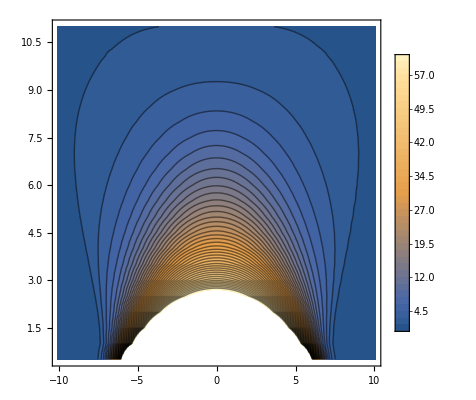

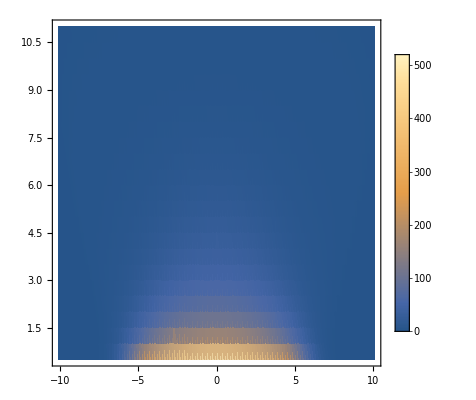

```mathematica
ListContourPlot[eplot,PlotLegends->Automatic,PlotRange->{{-10,10},{0.5,11}},Contours->40,ImageSize->400]

ListDensityPlot[eplot,PlotLegends->Automatic,PlotRange->All]
```

### Bulk pressure tau-x plot

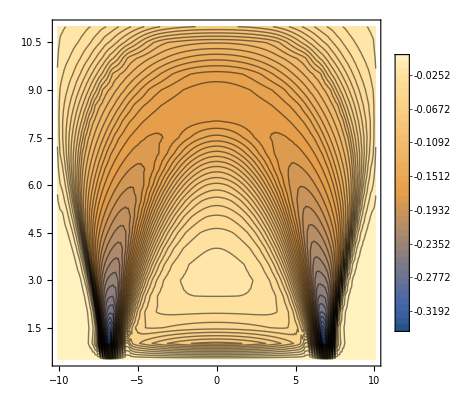

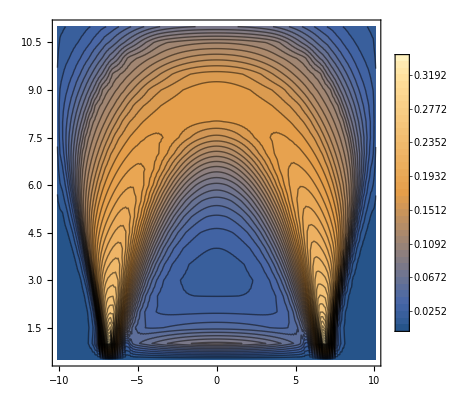

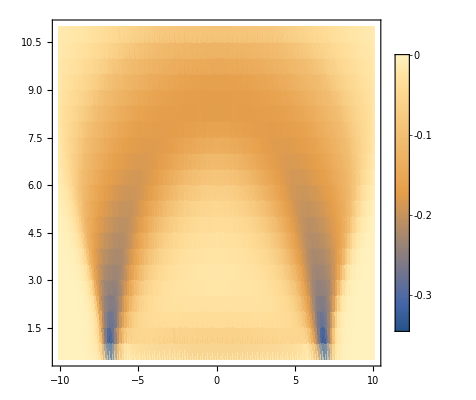

```mathematica
AbsPiplot= Piplot;
AbsPiplot[[All,3]]=Abs[Piplot[[All,3]]];

ListContourPlot[Piplot,PlotLegends->Automatic,PlotRange->{{-10,10},{0.5,11}},Contours->40,ImageSize->400]
ListContourPlot[AbsPiplot,PlotLegends->Automatic,PlotRange->{{-10,10},{0.5,11}},Contours->40,ImageSize->400]

ListDensityPlot[Piplot,PlotLegends->Automatic,PlotRange->All]
```

### Equilibrium pressure

```mathematica
(* Wuppertal-Budapest EoS *)
Pfunction[e_]:=Module[{answer},
e1=e;
e2=e1*e;
e3=e2*e;
e4=e3*e;
e5=e4*e;
e6=e5*e;
e7=e6*e;
e8=e7*e;
e9=e8*e;
e10=e9*e;
e11=e10*e;
e12=e11*e;

a0=-0.25181736420168666;
a1=9737.845799644809;
a2=1.077580993288114*10^6;
a3=3.1729694865420084*10^6;
a4=1.6357487344679043*10^6;
a5=334334.4309240126;
a6=41913.439282708554;
a7=6340.448389300905;
a8=141.5073484468774;
a9=0.7158279081255019;
a10=0.0009417586777847889;
a11=3.1188455176941583*10^-7;
a12=1.9531729608963267*10^-11;

a = a12*e12+a11*e11+a10*e10+a9*e9+a8*e8+a7*e7+a6*e6+a5*e5+a4*e4+a3*e3+a2*e2+a1*e1+a0;

b0=45829.44617893836;
b1=4.0574329080826794*10^6;
b2=2.0931169138134286*10^7;
b3=1.3512402226067686*10^7;
b4=1.7851642641834426*10^6;
b5=278581.2989342773;
b6=26452.34905933697;
b7=499.04919730607065;
b8=2.3405487982094204;
b9=0.002962497695527404;
b10=9.601103399348206*10^-7;
b11=5.928138360995685*10^-11;
b12=3.2581066229887368*10^-18;

b = b12*e12+b11*e11+b10*e10+b9*e9+b8*e8+b7*e7+b6*e6+b5*e5+b4*e4+b3*e3+b2*e2+b1*e1+b0;

answer = a/b;
Return[answer];
];

(* test *)
Pfunction[1.83756];

Pplot=eplot;
Pplot[[All,3]]=Pfunction[eplot[[All,3]]];
```

### Bulk inverse reynolds number

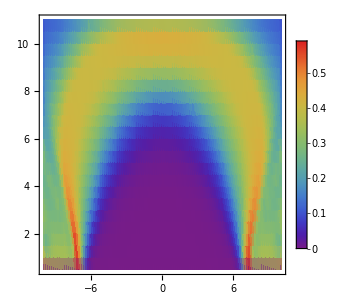

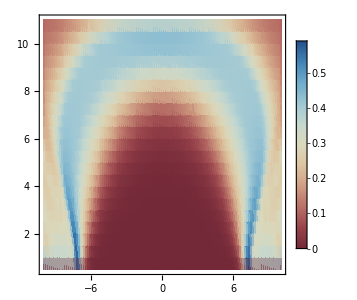

```mathematica
RinvPiplot = AbsPiplot;

RinvPiplot[[All,3]] = AbsPiplot[[All,3]] / Pplot[[All,3]];

(*ListContourPlot[RinvPiplot,PlotLegends->Automatic,PlotRange->{{-10,10},{0.5,11}},Contours->40,ImageSize->400];*)

ListDensityPlot[RinvPiplot,PlotLegends->Automatic,PlotRange->{{-10,10},{0.5,11}},ImageSize->300,ColorFunction->"Rainbow"]

ListDensityPlot[RinvPiplot,PlotLegends->Automatic,PlotRange->{{-10,10},{0.5,11}},ImageSize->300,ColorFunction->"RedBlueTones"]
```